# Mathematica code for implementation of the model for different cooperative ecological phenomena

This notebook contains source code for the following preprint article:

Droste MJ, Planqué R, Bruggeman FJ (2026) Emergent metabolic cooperation in communities of microbes that maximise growth rate by optimal protein expression.

Short description
This code contains the implementation of the models for different cooperative ecological phenomena discussed in the article. For each phenomenon, we implement a variant of the growth rate maximisation problem that compares the growth rate of two different microbial populations. Since each phenomenon is described by a different reaction network and/or parameter regime, we define a different set of parameters and an optimisation problem for each phenomenon. In all cases, a varying independent parameter results in a change in either the optimal community composition, the optimal metabolic strategy, or both. More information on the models for different cooperative ecological phenomena can be found in the Supplementary Appendices of the article.

Note: In some of the numerical solutions of the optimisations, numerical errors appear regarding convergence failure within a set number of iterations. The authors have checked that these errors arise because of the independency of the optimization problem on some of the variables in certain regimes. For instance, whenever mode 2 is the optimal solution, the enzyme and metabolite concentrations appearing in mode 1 can take any value within the feasible solution space without affecting the optimal solution. This sometimes results in a convergence failure. Since we want to use the optimisation problems to describe all these different regimes and these errors do not arise from numerical instabilities, we have decided to retain to the current algorithms and ignore these errors. This however also means that some of the results for mode 2 exclusively should be corrected: the growth rate of species B will become zero in this case, even though the optimisation will sometimes give a random value (as this does not affect the optimisation). Wherever necessary, we correct the simulation results by setting the growth rate of the consumer to zero explicitly when only mode 2 is used.

#### Settings for figures

```mathematica
SetOptions[{Plot,ListPlot,ListLogPlot,ListLinePlot,LogLinearPlot,ListLogLinearPlot},PlotStyle->Black,Frame->True,ImageSize->550,BaseStyle->{FontSize->22,FontColor->Black},FrameStyle->Directive[Black,22,Thickness->0.005], PlotStyle->ColorData[68,"ColorList"],AspectRatio->1];
StandardProlog={-Graphics-,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]};
```

#### Rate equations for both species

```mathematica
v[kcat_,s1_,s2_,e_,K1_,K2_,Keq_]:=kcat(e s1/K1(1-s2/(s1 Keq)))/(1+s1/K1+s2/K2)
```

```mathematica
vTA=v[kTA,s,sA,eTA,1,2,KeqT];
v1A=v[k1A,sA,p1,e1A,2,1,Keq];
v2A=v[k2A,sA,p2,e2A,2,1,Keq];
vRA=kRA fRA eRA;

vuB=v[kuB,p1,xB,euB,2,1,Keq];
v1B=v[k1B,xB,pB,e1B,1,2,Keq];
vRB=kRB fRB eRB;
```

## Solution to the general optimisation problem for a varying substrate concentration

#### Model parameters

```mathematica
ParamsvarS={p2->0.01,pB->0.2,
Keq->10^2,KeqT->1,
m2A->2,m1A->1,mRA->700,
m1B->1,mRB->700,
YsARA->200,Yp1sA->1,
YxBp1->1,YxBRB->200,
eTotA->1,eTA->0.1,
eTotB->1,
kTA->1000,k2A->185,k1A->1000,kRA->0.089,fRA->0.8,
kuB->1000,k1B->500,kRB->0.089,fRB->0.8,
BA0->1};
```

#### Optimisation problem: Maximise the growth rate of the producer for varying concentrations of S

Note that the biomass relation describing the coupling of the biomass of both species is written in a slightly different form and does not contain the densities ρ of both species. We have neglected these since they are assumed to be constant, so these can be scaled out of this relation. We are only interested in qualitative changes in the relative biomass fractions, that are not affected by these constant densities. We use this notation in all optimisation problems in this notebook.

```mathematica
ModelEquationsJoinedvarS[sv_]:=Join[{Evaluate[vRA/eTotA]},{
(*Positivity constraints*)sA>=0,p1>=0,xB>=0,e2A>=0,e1A>=0,eRA>=0,euB>=0,e1B>=0,eRB>=0,BB0>=0,
(*Enzyme constraints*)eTA+e2A+e1A+eRA<=eTotA,euB+e1B+eRB<=eTotB,
(*Steady states*)vTA==v2A+v1A+YsARA vRA,mRA vRA== m2A v2A+m1A v1A,BA0 Yp1sA v1A==BB0 vuB,YxBp1 vuB==v1B+YxBRB vRB,mRB vRB==m1B v1B,
(*Biomass relation*)BA0 Yp1sA v1A/vRA ==BB0/YxBp1 eTotB/eTotA(mRB/m1B+YxBRB)}]/.{s->sv}
OptimisationProblemFuncvarS[sv_?NumericQ]:=NMaximize[ModelEquationsJoinedvarS[sv]/.ParamsvarS,{sA,p1,xB,e2A,e1A,eRA,eRB,euB,e1B,BB0}]
```

#### Results

We run the optimisation problem for different values of the S concentration. After obtaining the results, we normalise the S concentration and the growth rate relative to the critical point where the shift from mode 2 to mode 1 initiates.

```mathematica
sstartvarS=0.01;
sendvarS=0.9;
sstepvarS=0.03;
OptimisationProblemSolvarS=Table[{s->sval,{λA->vRA/eTotA,λB->vRB/eTotB,BiomB->BB0,e1->e1A,e2->e2A,eRiboA->eRA,f1->v1A/(k1A e1A),f2->v2A/(k2A e2A),v2Aplot->v2A,v1Aplot->v1A}/.OptimisationProblemFuncvarS[sval][[2]]/.ParamsvarS/.{s->sval}}//Flatten,{sval,sstartvarS,sendvarS,sstepvarS}];
OptimisationProblemSolvarScorrec=OptimisationProblemSolvarS/. r_List/;Abs[BiomB/. r]<10^-5:>(r/. (λB->_):>(λB->0));
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

```mathematica
Scrit=s/. Last@Select[OptimisationProblemSolvarScorrec,(λB/. #)==0&];
Scritindex=FirstPosition[s/. OptimisationProblemSolvarScorrec,Scrit][[1]]
λAcrit=λA/. Last@Select[OptimisationProblemSolvarScorrec,(λB/. #)==0&];

Sendshift=s/. First@Select[OptimisationProblemSolvarScorrec,(e2/. #)<0.0001&];
Sendshiftindex=FirstPosition[s/. OptimisationProblemSolvarScorrec,Sendshift][[1]];
```

14

#### Figures

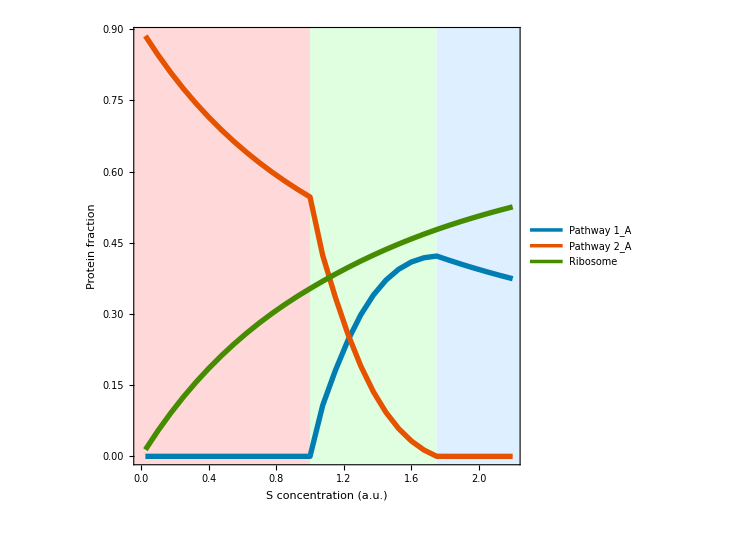

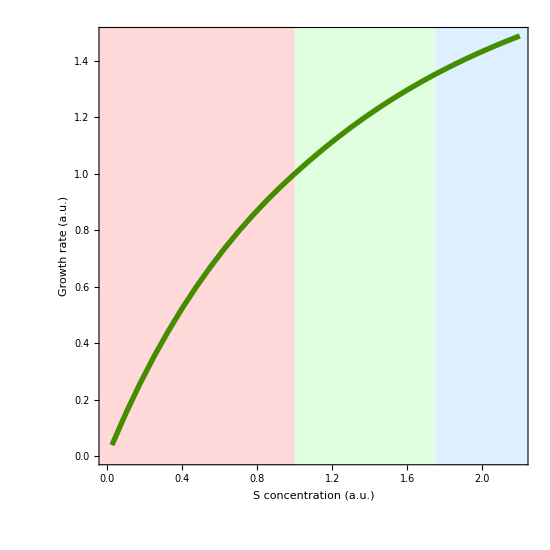

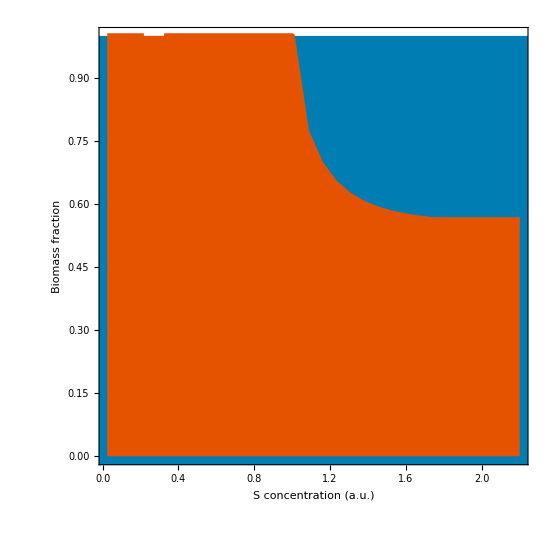

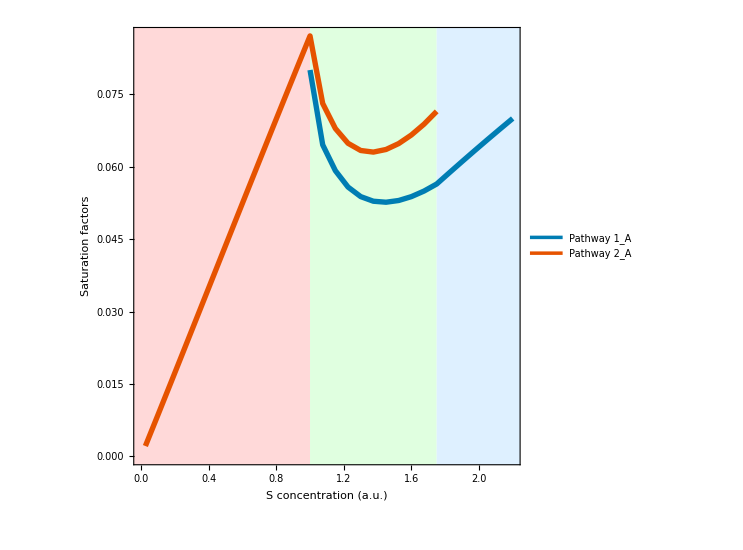

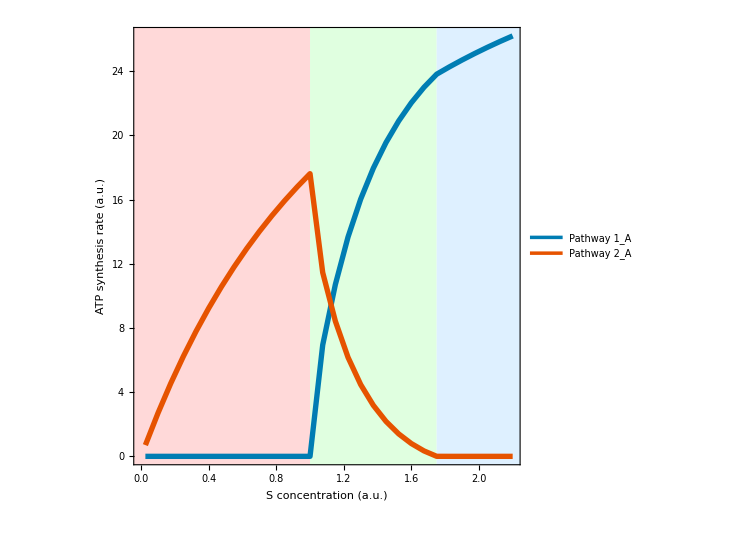

```mathematica
ListLinePlot[{{s/Scrit,e1}/.OptimisationProblemSolvarScorrec,{s/Scrit,e2}/.OptimisationProblemSolvarScorrec,{s/Scrit,eRiboA}/.OptimisationProblemSolvarScorrec},FrameLabel->{"S concentration (a.u.)","Protein fraction"},PlotLegends->Placed[PointLegend[{"Pathway 1_A","Pathway 2_A" ,"Ribosome"},LegendFunction->"Frame",LabelStyle->{FontFamily->"Helvetica",FontSize->18},LegendMarkerSize->{20,15}],{0.2,0.55}],PlotStyle->{{ColorData[68,"ColorList"][[1]],Thickness[0.007]},{ColorData[68,"ColorList"][[2]],Thickness[0.007]},{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{-1,-1},{1,2}]},{LightGreen,Rectangle[{1,-1},{Sendshift/Scrit,2}]},{LightBlue,Rectangle[{Sendshift/Scrit,-1},{8,2}]}},ImagePadding->{{80,10},{70,10}}]

ListLinePlot[{{s/Scrit,λA/λAcrit}/.OptimisationProblemSolvarScorrec},FrameLabel->{"S concentration (a.u.)","Growth rate (a.u.)"},PlotStyle->{{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{-1,-1},{1,2}]},{LightGreen,Rectangle[{1,-1},{Sendshift/Scrit,2}]},{LightBlue,Rectangle[{Sendshift/Scrit,-1},{8,2}]}},ImagePadding->{{80,10},{70,10}}]

biomassplotvarS=ListLinePlot[{s/Scrit,BA0/(BA0+BiomB)}/.OptimisationProblemSolvarScorrec/.ParamsvarS,FrameLabel->{"S concentration (a.u.)","Biomass fraction"},PlotRange->{All,{0,1}},PlotRangePadding->0,FrameStyle->Directive[Black,40,Thickness->0.005],PlotStyle->{ColorData[68,"ColorList"][[2]],Thickness[0.007]},Filling->Bottom,FillingStyle->{ColorData[68,"ColorList"][[2]]},Prolog->{ColorData[68,"ColorList"][[1]],Rectangle[{-1,-1},{3,1}]}]

ListLinePlot[{{s/Scrit,f1}/.OptimisationProblemSolvarScorrec[[Scritindex;;]],{s/Scrit,f2}/.OptimisationProblemSolvarScorrec[[;;Sendshiftindex]]},PlotLegends->Placed[PointLegend[{"Pathway 1_A","Pathway 2_A" },LegendFunction->"Frame",LabelStyle->{FontFamily->"Helvetica",FontSize->18},LegendMarkerSize->{20,15}],{0.2,0.82}],FrameLabel->{"S concentration (a.u.)","Saturation factors"},PlotStyle->{{ColorData[68,"ColorList"][[1]],Thickness[0.007]},{ColorData[68,"ColorList"][[2]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{-1,-1},{1,2}]},{LightGreen,Rectangle[{1,-1},{Sendshift/Scrit,2}]},{LightBlue,Rectangle[{Sendshift/Scrit,-1},{8,2}]}},ImagePadding->{{80,10},{70,10}}]

ListLinePlot[{{s/Scrit,m1A v1Aplot}/.OptimisationProblemSolvarScorrec/.ParamsvarS,{s/Scrit,m2A v2Aplot}/.OptimisationProblemSolvarScorrec/.ParamsvarS},PlotLegends->Placed[PointLegend[{"Pathway 1_A","Pathway 2_A"},LegendFunction->"Frame",LabelStyle->{FontFamily->"Helvetica",FontSize->18},LegendMarkerSize->{20,15}],{0.2,0.67}],FrameLabel->{"S concentration (a.u.)","ATP synthesis rate (a.u.)"},PlotStyle->{{ColorData[68,"ColorList"][[1]],Thickness[0.007]},{ColorData[68,"ColorList"][[2]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{-1,-2},{1,100}]},{LightGreen,Rectangle[{1,-2},{Sendshift/Scrit,100}]},{LightBlue,Rectangle[{Sendshift/Scrit,-2},{8,100}]}},ImagePadding->{{80,10},{70,10}}]
```

## Model and results for mutualism and obligate syntrophy

To model mutualistic interactions, the cross-feeding of P_1 should be beneficial to both the producer and the consumer. To make this effect apparent in both species, we set the equilibrium constant to Keq=10 for all reactions except the transport of S, and we set K_p1^A = 0.01 mM.

We study the community as function of the affinity of the producer for P_1, which is described by the inverse of the parameter K_p1^B in our model (a lower Michaelis constant implies a higher affinity). Therefore, we write this as 1/K_m  in the model, such that an increase in K_m describes an increasing affinity.

These two adjustments require two adjusted rate equations for the fluxes v1A and vUB, which are given below. These are also used in all other simulations as function of the affinity of the producer.

```mathematica
v1AKm=v[k1A,sA,p1,e1A,2,0.01,Keq];
vuBKm=v[kuB,p1,xB,euB,1/Km,1,Keq];
```

### Mutualism

#### Model parameters

```mathematica
ParamsMut={s->0.3,p2->0.1,pB->0.02,
Keq->10,KeqT->1,
m2A->2,m1A->1,mRA->700,
m1B->1,mRB->700,
YsARA->200,Yp1sA->1,
YxBp1->1,YxBRB->200,
eTotA->1,eTA->0.1,
eTotB->1,
kTA->1000,k2A->185,k1A->1000,kRA->0.089,fRA->0.8,
kuB->1000,k1B->500,kRB->0.089,fRB->0.8,
BA0->1};
```

#### Optimisation problem: Maximise the growth rate of the producer for varying affinity of the consumer

```mathematica
ModelEquationsJoinedMut[Kminv_]:=Join[{Evaluate[vRA/eTotA]},
{(*Positivity constraints*)sA>=0,p1>=0,xB>=0,e1A>=0,eRA>=0,euB>=0,e1B>=0,eRB>=0,BB0>=0,
(*Enzyme constraints*)eTA+e1A+eRA<=eTotA,euB+e1B+eRB<=eTotB,
(*Steady states*)vTA==v1AKm+YsARA vRA,mRA vRA== m1A v1AKm,BA0 Yp1sA v1AKm==BB0 vuBKm,YxBp1 vuBKm==v1B+YxBRB vRB,mRB vRB==m1B v1B,
(*Biomass relation*)BA0 YxBp1 Yp1sA mRA/m1A ==BB0 eTotB/eTotA(mRB/m1B+YxBRB)}]/.{Km->Kminv}
OptimisationProblemFuncMut[Kminv_?NumericQ]:=NMaximize[ModelEquationsJoinedMut[Kminv]/.ParamsMut,{sA,p1,xB,e1A,eRA,eRB,euB,e1B,BB0}]
```

#### Results

We run the optimisation problem for different values of the affinity of the consumer. After obtaining the results, we normalise the P_1 concentration and the growth rate relative to the point where K_m = 0.01. This point is picked randomly and indicates the state of the population with only the producer.

```mathematica
OptimisationProblemSolMut=Table[{Kminv->Kminvval,{p1v->p1,λ->vRA/eTotA}/.OptimisationProblemFuncMut[Kminvval][[2]]/.ParamsMut/.{Km->Kminvval}}//Flatten,{Kminvval,{0.004,0.005,0.01,0.02,0.05,0.08,0.1,0.2,0.5,0.8,1,2,5,10}}];
```

```mathematica
P1initMut=p1v/. Last@Select[OptimisationProblemSolMut,(Kminv/. #)==0.01&];
λinitMut=λ/.  Last@Select[OptimisationProblemSolMut,(Kminv/. #)==0.01&];
```

#### Figures

```mathematica
ListLogLinearPlot[{Kminv,p1v/P1initMut}/.OptimisationProblemSolMut,FrameLabel->{"Affinity of consumer (a.u.)","P_1 concentration (a.u.)"},Joined->True,Prolog->StandardProlog,PlotStyle->{{ColorData[68,"ColorList"][[1]],Thickness[0.007]}},ImagePadding->{{70,10},{70,10}}]

ListLogLinearPlot[{Kminv,λ/λinitMut}/.OptimisationProblemSolMut,FrameLabel->{"Affinity of consumer (a.u.)","Growth rate (a.u.)"},Joined->True,Prolog->StandardProlog,PlotStyle->{{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},ImagePadding->{{70,10},{70,10}}]

ListLinePlot[{p1v/P1initMut,λ/λinitMut}/.OptimisationProblemSolMut,FrameLabel->{ "P_1 concentration (a.u.)","Growth rate (a.u.)"},PlotRange->{All,All},PlotStyle->{ColorData[68,"ColorList"][[3]],Thickness[0.007]},Prolog->StandardProlog]
```

-Graphics-

-Graphics-

-Graphics-

### Obligate syntrophy

To model obligate syntrophy, we use the exact same model as for mutualism, except we simulate it at lower values of the affinity of the consumer. This approximates the scenario close to thermodynamic equilibrium. This is explained in more detail in the Supplementary Appendices.

#### Results

```mathematica
OptimisationProblemSolOblSyn=Table[{Kminv->Kminvval,{p1v->p1,λ->vRA/eTotA}/.OptimisationProblemFuncMut[Kminvval][[2]]/.ParamsMut/.{Km->Kminvval}}//Flatten,{Kminvval,{0.000001,0.000002,0.000005,0.00001,0.00002,0.00005,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.01,0.05,0.1}}];
```

#### Figures

```mathematica
ListLogLinearPlot[{Kminv,p1v/P1initMut}/.OptimisationProblemSolOblSyn,FrameLabel->{"Affinity of consumer (a.u.)","P_1 concentration (a.u.)"},Joined->True,Prolog->StandardProlog,PlotStyle->{{ColorData[68,"ColorList"][[1]],Thickness[0.007]}},ImagePadding->{{70,6},{70,10}}]

ListLogLinearPlot[{Kminv,λ/λinitMut}/.OptimisationProblemSolOblSyn,FrameLabel->{"Affinity of consumer (a.u.)","Growth rate (a.u.)"},Joined->True,Prolog->StandardProlog,PlotStyle->{{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},ImagePadding->{{70,6},{70,10}}]

ListLinePlot[{p1v/P1initMut,λ/λinitMut}/.OptimisationProblemSolOblSyn,FrameLabel->{ "P_1 concentration (a.u.)","Growth rate (a.u.)"},PlotRange->{All,All},PlotStyle->{ColorData[68,"ColorList"][[3]],Thickness[0.007]},Prolog->StandardProlog]
```

-Graphics-

-Graphics-

-Graphics-

## Model and results for facultative syntrophy

#### Model parameters

```mathematica
ParamsFacSyn={s->0.3,p2->0.5,pB->0.02,
Keq->10,KeqT->1,
m2A->2,m1A->1,mRA->700,
m1B->1,mRB->700,
YsARA->200,Yp1sA->1,
YxBp1->1,YxBRB->200,
eTotA->1,eTA->0.1,
eTotB->1,
kTA->1000,k2A->185,k1A->1000,kRA->0.089,fRA->0.8,
kuB->1000,k1B->500,kRB->0.089,fRB->0.8,
BA0->1};
```

#### Optimisation problem: Maximise the growth rate of the producer for varying affinity of the consumer

```mathematica
ModelEquationsJoinedFacSyn[Kminv_]:=Join[{Evaluate[vRA/eTotA]},
{(*Positivity constraints*)sA>=0,p1>=0,xB>=0,e2A>=0,e1A>=0,eRA>=0,euB>=0,e1B>=0,eRB>=0,BB0>=0,
(*Enzyme constraints*)eTA+e2A+e1A+eRA<=eTotA,euB+e1B+eRB<=eTotB,
(*Steady states*)vTA==v2A+v1AKm+YsARA vRA,mRA vRA== m2A v2A+m1A v1AKm,BA0 Yp1sA v1AKm==BB0 vuBKm,YxBp1 vuBKm==v1B+YxBRB vRB,mRB vRB==m1B v1B,
(*Biomass relation*)BA0 Yp1sA v1AKm/vRA ==BB0/YxBp1 eTotB/eTotA(mRB/m1B+YxBRB)}]/.{Km->Kminv}
OptimisationProblemFuncFacSyn[Kminv_?NumericQ]:=NMaximize[ModelEquationsJoinedFacSyn[Kminv]/.ParamsFacSyn,{sA,p1,xB,e1A,e2A,eRA,eRB,euB,e1B,BB0}]
```

#### Results

We run the optimisation problem for different values of the affinity of the consumer. After obtaining the results, we normalise the growth rate relative to the point where the switch from mode 2 to mode 1 occurs.

```mathematica
OptimisationProblemSolFacSyn=Table[{Kminv->Kminvval,{p1v->p1,λA->vRA/eTotA,λB->vRB/eTotB,BiomB->BB0,e1->e1A,e2->e2A,eRiboA->eRA}/.OptimisationProblemFuncFacSyn[Kminvval][[2]]/.ParamsFacSyn/.{Kminv->Kminvval}}//Flatten,{Kminvval,{0.004,0.005,0.01,0.02,0.05,0.08,0.1,0.2,0.5,0.8,1,1.5,1.7,1.8,1.9,2,5,10,50}}];
OptimisationProblemSolFacSyncorrec=OptimisationProblemSolFacSyn/. r_List/;Abs[BiomB/. r]<10^-6:>(r/. {(λB->_):>(λB->0),(p1v->_):>(p1v->0)});
```

NMaximize::nnum: The function value Indeterminate is not a number at {BB0,e1A,e1B,e2A,eRA,eRB,euB,p1,sA,xB} = {0.000521854,0.,0.0212762,0.,0.,0.175254,0.483633,96274.,0.254878,31594.3}.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

NMaximize::nnum: The function value ∞ is not a number at {BB0,e1A,e1B,e2A,eRA,eRB,euB,p1,sA,xB} = {3.59942×10^-8,0.0000583635,0.00115312,0.159008,0.,0.0210531,6.26787×10^-6,127011.,0.270187,50856.2}.

```mathematica
λswitchFacSyn=λA/.Last@Select[OptimisationProblemSolFacSyncorrec,(λB/. #)==0&];
KminvswitchFacSyn=Kminv/.Last@Select[OptimisationProblemSolFacSyncorrec,(λB/. #)==0&];
```

#### Figures

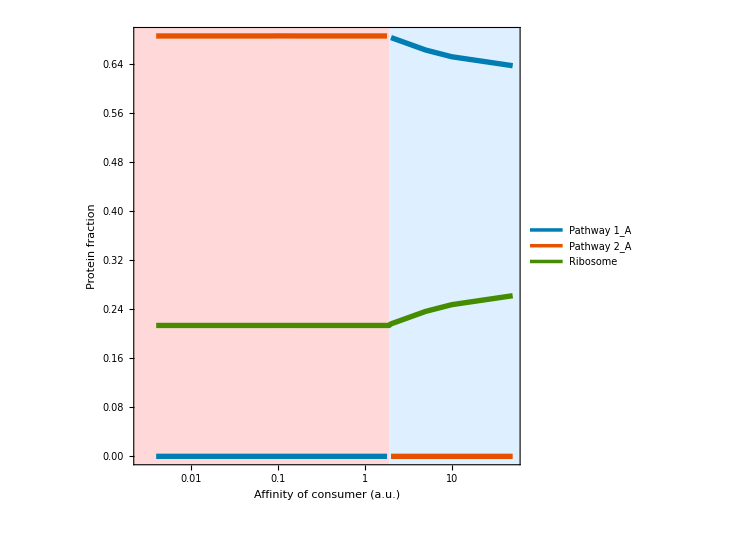

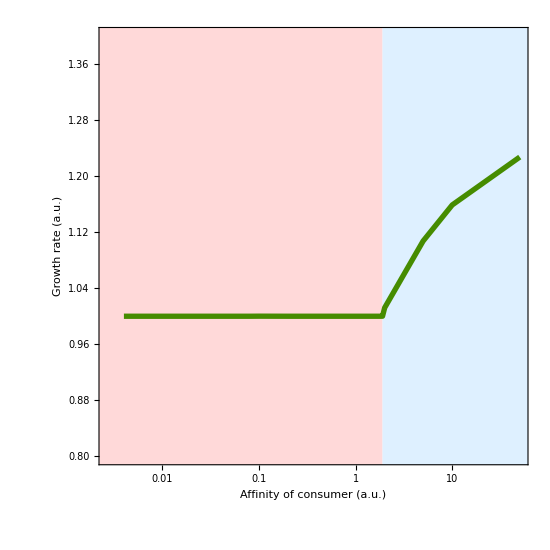

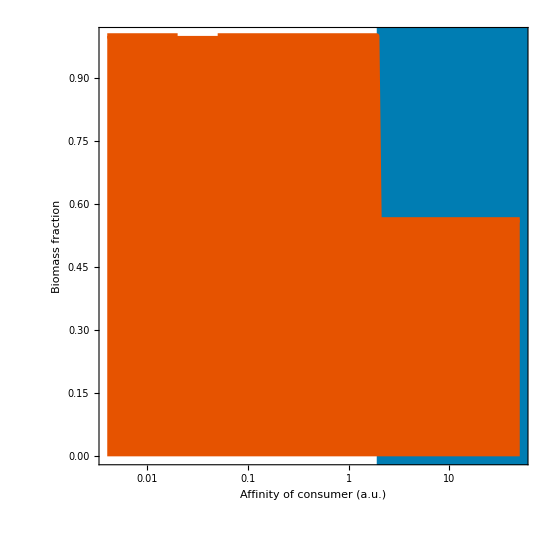

```mathematica
ListLogLinearPlot[{{Kminv,e1}/.OptimisationProblemSolFacSyncorrec/.{x_,y_}/;x==KminvswitchFacSyn->{x,Indeterminate},{Kminv,e2}/.OptimisationProblemSolFacSyncorrec/.{x_,y_}/;x==KminvswitchFacSyn->{x,Indeterminate},{Kminv,eRiboA}/.OptimisationProblemSolFacSyncorrec},FrameLabel->{"Affinity of consumer (a.u.)","Protein fraction"},Joined->True,PlotLegends->Placed[PointLegend[{"Pathway 1_A","Pathway 2_A" ,"Ribosome"},LegendFunction->"Frame",LabelStyle->{FontFamily->"Helvetica",FontSize->18},LegendMarkerSize->{20,15}],{0.2,0.6}],PlotStyle->{{ColorData[68,"ColorList"][[1]],Thickness[0.007]},{ColorData[68,"ColorList"][[2]],Thickness[0.007]},{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{Log[0.0001],-1},{Log[KminvswitchFacSyn],2}]},{LightBlue,Rectangle[{Log[KminvswitchFacSyn],-1},{8,2}]}},ImagePadding->{{70,10},{70,10}}]

ListLogLinearPlot[{{Kminv,λA/λswitchFacSyn}/.OptimisationProblemSolFacSyncorrec},Joined->True,PlotRange->{All,{0.8,1.4}},FrameLabel->{"Affinity of consumer (a.u.)","Growth rate (a.u.)"},PlotStyle->{{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{Log[0.0001],-1},{Log[KminvswitchFacSyn],2}]},{LightBlue,Rectangle[{Log[KminvswitchFacSyn],-1},{8,2}]}},ImagePadding->{{70,10},{70,10}}]

biomassplotfacsyn=ListLogLinearPlot[{Kminv,BA0/(BA0+BiomB)}/.OptimisationProblemSolFacSyncorrec/.ParamsFacSyn,Joined->True,FrameLabel->{"Affinity of consumer (a.u.)","Biomass fraction"},PlotRange->{All,{0,1}},PlotRangePadding->0,PlotStyle->{ColorData[68,"ColorList"][[2]],Thickness[0.007]},Filling->Bottom,FillingStyle->{ColorData[68,"ColorList"][[2]]},FrameStyle->Directive[Black,40,Thickness->0.005],Prolog->{ColorData[68,"ColorList"][[1]],Rectangle[{Log[KminvswitchFacSyn],-1},{8,2}]}]
```

## Model and results for syntrophic interactions with multiple consumers

To model syntrophy with two consumers B, C, we need to implement an additional consuming species. We extend the optimisation problem below to include this species. Its rate equations and parameters are defined below. They are similar to those of species B, such that both communities attain similar growth rates.

Since all parameters of species C are fixed, the community consisting of species A and C has a constant (optimal) growth rate, as can be seen in the plots below. For sufficiently high affinity of species B for P1, this growth rate is exceeded, and the optimal strategy and community composition switch.

#### Rate equations for species C

```mathematica
vuC=v[kuC,p2,xC,euC,30,1,Keq];
v2C=v[k2C,xC,pC,e2C,1,2,Keq];
vRC=kRC fRC eRC;
```

#### Model parameters

```mathematica
ParamsSyn2Cons={s->0.35,pC->0.02,pB->0.02,
Keq->10,KeqT->1,
m2A->2,m1A->1,mRA->700,
m1B->1,mRB->700,
m2C->1,mRC->700,
YsARA->200,Yp1sA->1,Yp2sA->1,
YxBp1->1,YxBRB->200,
YxCp2->3,YxCRC->200,
eTotA->1,eTA->0.1,
eTotB->1,
eTotC->1,
kTA->1000,k2A->185,k1A->1000,kRA->0.089,fRA->0.8,
kuB->1000,k1B->500,kRB->0.089,fRB->0.8,
kuC->1000,k2C->500,kRC->0.089,fRC->0.8,
BA0->1};
```

#### Optimisation problem: Maximise the growth rate of the producer for varying affinity of the consumer B and fixed species C

```mathematica
ModelEquationsJoinedSyn2Cons[Kminv_]:=Join[{Evaluate[vRA/eTotA]},
{(*Positivity constraints*)sA>=0,p1>=0,xB>=0,p2>=0,xC>=0,e2A>=0,e1A>=0,eRA>=0,euB>=0,e1B>=0,eRB>=0,BB0>=0,euC>=0,e2C>=0,eRC>=0,BC0>=0,
(*Enzyme constraints*)eTA+e2A+e1A+eRA<=eTotA,euB+e1B+eRB<=eTotB,euC+e2C+eRC<=eTotC,
(*Steady states*)vTA==v2A+v1AKm+YsARA vRA,mRA vRA== m2A v2A+m1A v1AKm,BA0 Yp1sA v1AKm==BB0 vuBKm,YxBp1 vuBKm==v1B+YxBRB vRB,mRB vRB==m1B v1B,
BA0 Yp2sA v2A==BC0 vuC,YxCp2 vuC==v2C+YxCRC vRC,mRC vRC==m2C v2C,
(*Biomass relations*)BA0 Yp1sA v1AKm/vRA ==BB0/YxBp1 eTotB/eTotA(mRB/m1B+YxBRB),BA0 Yp2sA v2A/vRA ==BC0/YxCp2 eTotC/eTotA(mRC/m2C+YxCRC)}]/.{Km->Kminv}
OptimisationProblemFuncSyn2Cons[Kminv_?NumericQ]:=NMaximize[ModelEquationsJoinedSyn2Cons[Kminv]/.ParamsSyn2Cons,{sA,p1,xB,p2,xC,e1A,e2A,eRA,eRB,euB,e1B,euC,e2C,eRC,BB0,BC0}]
```

#### Results

We run the optimisation problem for different values of the affinity of the consumer B. After obtaining the results, we normalise the growth rate relative to the point where the switch from mode 2 to mode 1 for facultative syntrophy occurs.

```mathematica
OptimisationProblemSolSyn2Cons=Table[{Kminv->Kminvval,{p1v->p1,λA->vRA/eTotA,λB->vRB/eTotB,BiomB->BB0,BiomC->BC0,e1->e1A,e2->e2A,eRiboA->eRA}/.OptimisationProblemFuncSyn2Cons[Kminvval][[2]]/.ParamsSyn2ConsTest/.{Kminv->Kminvval}}//Flatten,{Kminvval,{0.005,0.01,0.05,0.1,0.5,1,1.5,4,5,5.5,6,6.2,6.5,6.7,7.2,8,10,25,60}}];
OptimisationProblemSolSyn2Conscorrec=OptimisationProblemSolSyn2Cons/. r_List/;Abs[BiomB/. r]<10^-6:>(r/. {(λB->_):>(λB->0),(p1v->_):>(p1v->0)});
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

```mathematica
KminvswitchSyn2Cons=Kminv/.Last@Select[OptimisationProblemSolSyn2Conscorrec,(λB/. #)==0&];
KminvswitchSyn2Consindex=FirstPosition[Kminv/. OptimisationProblemSolSyn2Conscorrec,KminvswitchSyn2Cons][[1]];
```

#### Figures

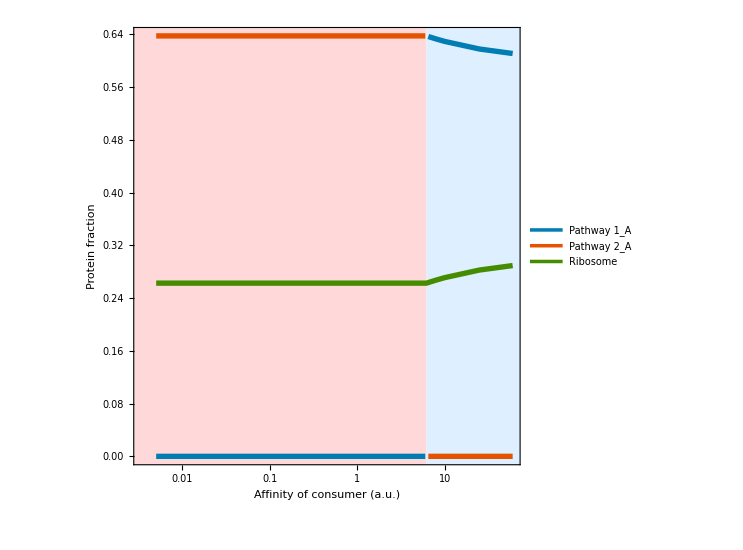

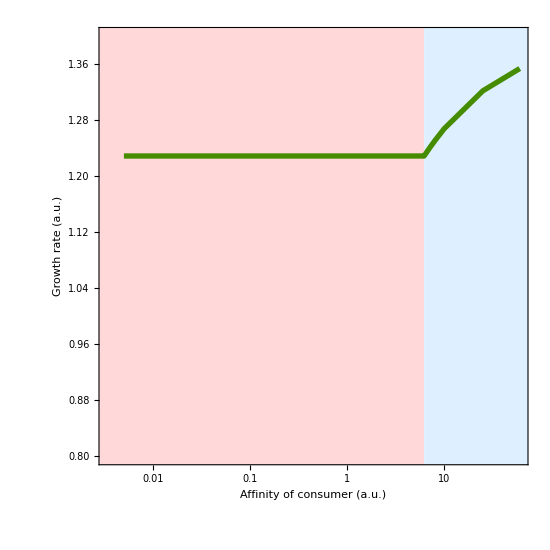

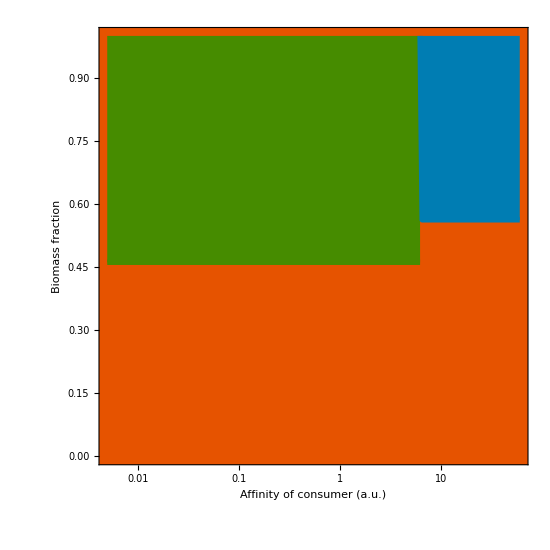

```mathematica
ListLogLinearPlot[{{Kminv,e1}/.OptimisationProblemSolSyn2Conscorrec/.{x_,y_}/;x==KminvswitchSyn2Cons->{x,Indeterminate},{Kminv,e2}/.OptimisationProblemSolSyn2Conscorrec/.{x_,y_}/;x==KminvswitchSyn2Cons->{x,Indeterminate},{Kminv,eRiboA}/.OptimisationProblemSolSyn2Conscorrec},FrameLabel->{"Affinity of consumer (a.u.)","Protein fraction"},Joined->True,PlotLegends->Placed[PointLegend[{"Pathway 1_A","Pathway 2_A" ,"Ribosome"},LegendFunction->"Frame",LabelStyle->{FontFamily->"Helvetica",FontSize->18},LegendMarkerSize->{20,15}],{0.2,0.6}],PlotStyle->{{ColorData[68,"ColorList"][[1]],Thickness[0.007]},{ColorData[68,"ColorList"][[2]],Thickness[0.007]},{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{Log[0.0001],-1},{Log[KminvswitchSyn2Cons],2}]},{LightBlue,Rectangle[{Log[KminvswitchSyn2Cons],-1},{8,2}]}},ImagePadding->{{70,10},{70,10}}]

ListLogLinearPlot[{{Kminv,λA/λswitchFacSyn}/.OptimisationProblemSolSyn2Conscorrec},Joined->True,FrameLabel->{"Affinity of consumer (a.u.)","Growth rate (a.u.)"},PlotRange->{All,{0.8,1.4}},PlotStyle->{{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{Log[0.0001],-1},{Log[KminvswitchSyn2Cons],2}]},{LightBlue,Rectangle[{Log[KminvswitchSyn2Cons],-1},{8,2}]}},ImagePadding->{{70,10},{70,10}}]

biomassplotsyn2con=ListLogLinearPlot[{{Kminv,BA0/(BA0+BiomC)}/.OptimisationProblemSolSyn2Conscorrec[[;;KminvswitchSyn2Consindex]],{Kminv,BA0/(BA0+BiomB)}/.OptimisationProblemSolSyn2Conscorrec[[KminvswitchSyn2Consindex;;]]}/.ParamsSyn2Cons,Joined->True,FrameLabel->{"Affinity of consumer (a.u.)","Biomass fraction"},PlotRange->{All,{0,1}},PlotRangePadding->0,PlotStyle->{{ColorData[68,"ColorList"][[3]],Thickness[0.007]},{ColorData[68,"ColorList"][[1]],Thickness[0.007]}},Filling->{1->Top,2->Top},FillingStyle->{{ColorData[68,"ColorList"][[3]]},{ColorData[68,"ColorList"][[1]]}},FrameStyle->Directive[Black,40,Thickness->0.005],Prolog->{ColorData[68,"ColorList"][[2]],Rectangle[{Log[10^-5],-1},{8,2}]}]
```

## Model and results for resource allocation over mixed strategies

To model resource allocation over mixed strategies in both populations, we need to make sure that we simulate the model in the regime where a combination of both modes is the optimal strategy. By increasing the S concentration to 0.5 mM, we are in this regime. Furthermore, we decrease P_2 such that the product inhibition of both modes is comparable. In this regime, the model exhibits a gradual shift instead of a discrete switch between both modes.

#### Model parameters

```mathematica
ParamsMixStrat={s->0.5,p2->0.01,pB->0.02,
Keq->10,KeqT->1,
m2A->2,m1A->1,mRA->700,
m1B->1,mRB->700,
YsARA->200,Yp1sA->1,
YxBp1->1,YxBRB->200,
eTotA->1,eTA->0.1,
eTotB->1,
kTA->1000,k2A->185,k1A->1000,kRA->0.089,fRA->0.8,
kuB->1000,k1B->500,kRB->0.089,fRB->0.8,
BA0->1};
```

#### Optimisation problem: Maximise the growth rate of the producer for varying affinity of the consumer

```mathematica
ModelEquationsJoinedMixStrat[Kminv_]:=Join[{Evaluate[vRA/eTotA]},
{(*Positivity constraints*)sA>=0,p1>=0,xB>=0,e2A>=0,e1A>=0,eRA>=0,euB>=0,e1B>=0,eRB>=0,BB0>=0,
(*Enzyme constraints*)eTA+e2A+e1A+eRA<=eTotA,euB+e1B+eRB<=eTotB,
(*Steady states*)vTA==v2A+v1A+YsARA vRA,mRA vRA== m2A v2A+m1A v1A,BA0 Yp1sA v1A==BB0 vuBKm,YxBp1 vuBKm==v1B+YxBRB vRB,mRB vRB==m1B v1B,
(*Biomass relation*)BA0 Yp1sA v1A/vRA ==BB0/YxBp1 eTotB/eTotA(mRB/m1B+YxBRB)}]/.{Km->Kminv}
OptimisationProblemFuncMixStrat[Kminv_?NumericQ]:=NMaximize[ModelEquationsJoinedMixStrat[Kminv]/.ParamsMixStrat,{sA,p1,xB,e1A,e2A,eRA,eRB,euB,e1B,BB0}]
```

#### Results

We run the optimisation problem for different values of the affinity of the consumer. After obtaining the results, we normalise the growth rate relative to the point where the shift from mode 2 to mode 1 initiates.

```mathematica
OptimisationProblemSolMixStrat=Table[{Kminv->Kminvval,{p1v->p1,λA->vRA/eTotA,λB->vRB/eTotB,BiomB->BB0,e1->e1A,e2->e2A,eRiboA->eRA}/.OptimisationProblemFuncMixStrat[Kminvval][[2]]/.ParamsMixStrat/.{Kminv->Kminvval}}//Flatten,{Kminvval,{0.1,0.2,0.4,0.5,0.7,0.8,1,1.5,2,4,5,8.5,10}}];
OptimisationProblemSolMixStratcorrec=OptimisationProblemSolMixStrat/. r_List/;Abs[BiomB/. r]<10^-6:>(r/. {(λB->_):>(λB->0),(p1v->_):>(p1v->0)});
```

```mathematica
λinitshiftMixStrat=λA/.Last@Select[OptimisationProblemSolMixStratcorrec,(λB/. #)==0&];
KminvinitshiftMixStrat=Kminv/.Last@Select[OptimisationProblemSolMixStratcorrec,(λB/. #)==0&];
KminvendshiftMixStrat=Kminv/.First@Select[OptimisationProblemSolMixStratcorrec,(e2/. #)<0.0001&];
```

#### Figures

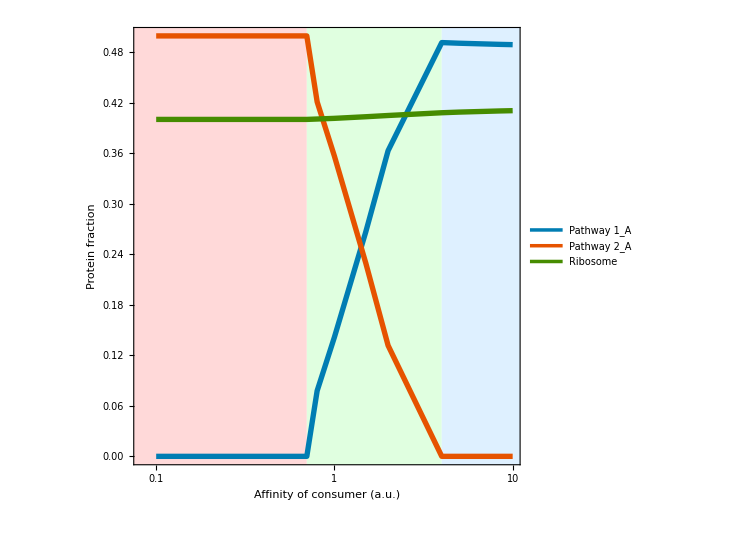

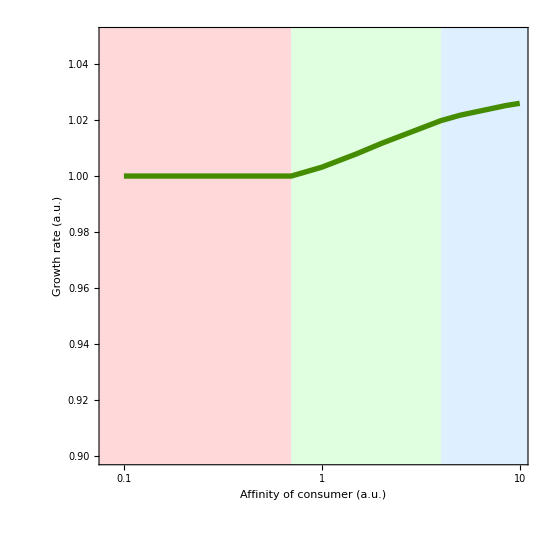

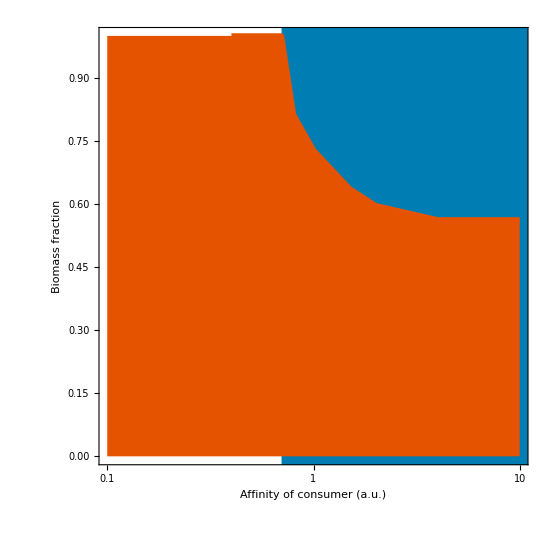

```mathematica
ListLogLinearPlot[{{Kminv,e1}/.OptimisationProblemSolMixStratcorrec,{Kminv,e2}/.OptimisationProblemSolMixStratcorrec,{Kminv,eRiboA}/.OptimisationProblemSolMixStratcorrec},FrameLabel->{"Affinity of consumer (a.u.)","Protein fraction"},Joined->True,PlotLegends->Placed[PointLegend[{"Pathway 1_A","Pathway 2_A" ,"Ribosome"},LegendFunction->"Frame",LabelStyle->{FontFamily->"Helvetica",FontSize->18},LegendMarkerSize->{20,15}],{0.2,0.6}],PlotStyle->{{ColorData[68,"ColorList"][[1]],Thickness[0.007]},{ColorData[68,"ColorList"][[2]],Thickness[0.007]},{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{Log[0.0001],-1},{Log[KminvinitshiftMixStrat],2}]},{LightGreen,Rectangle[{Log[KminvinitshiftMixStrat],-1},{Log[KminvendshiftMixStrat],2}]},{LightBlue,Rectangle[{Log[KminvendshiftMixStrat],-1},{8,2}]}},ImagePadding->{{80,10},{70,10}}]

ListLogLinearPlot[{{Kminv,λA/λinitshiftMixStrat}/.OptimisationProblemSolMixStratcorrec},Joined->True,FrameLabel->{"Affinity of consumer (a.u.)","Growth rate (a.u.)"},PlotRange->{All,{0.9,1.05}},PlotStyle->{{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{Log[0.0001],-1},{Log[KminvinitshiftMixStrat],2}]},{LightGreen,Rectangle[{Log[KminvinitshiftMixStrat],-1},{Log[KminvendshiftMixStrat],2}]},{LightBlue,Rectangle[{Log[KminvendshiftMixStrat],-1},{8,2}]}},ImagePadding->{{80,10},{70,10}}]

biomassplotmixstrat=ListLogLinearPlot[{Kminv,BA0/(BA0+BiomB)}/.OptimisationProblemSolMixStratcorrec/.ParamsMixStrat,Joined->True,FrameLabel->{"Affinity of consumer (a.u.)","Biomass fraction"},PlotRange->{All,{0,1}},FrameStyle->Directive[Black,40,Thickness->0.005],PlotRangePadding->0,PlotStyle->{ColorData[68,"ColorList"][[2]],Thickness[0.007]},Filling->Bottom,FillingStyle->{ColorData[68,"ColorList"][[2]]},Prolog->{ColorData[68,"ColorList"][[1]],Rectangle[{Log[KminvinitshiftMixStrat],-1},{8,2}]}]
```

## Solution to the general model for varying biomass yield of the consumer

Here we vary the biomass yield of the consumer for its carbon substrate as independent parameter.

#### Model parameters

```mathematica
Params1varYield={s->0.3,p2->0.1,pB->0.02,
Keq->10,KeqT->1,
m2A->2,m1A->1,mRA->700,
m1B->1,mRB->700,
YsARA->200,Yp1sA->1,
YxBp1->1,
eTotA->1,eTA->0.1,
eTotB->1,
kTA->1000,k2A->185,k1A->1000,kRA->0.089,fRA->0.8,
kuB->1000,k1B->500,kRB->0.089,fRB->0.8,
BA0->1};
```

#### Optimisation problem: Maximise the growth rate of the producer for varying biomass yield of the consumer

```mathematica
ModelEquationsJoinedvarYield[YxBRBv_]:=Join[{Evaluate[vRA/eTotA]},
{(*Positivity constraints*)sA>=0,p1>=0,xB>=0,e1A>=0,eRA>=0,euB>=0,e1B>=0,eRB>=0,BB0>=0,
(*Enzyme constraints*)eTA+e1A+eRA<=eTotA,euB+e1B+eRB<=eTotB,
(*Steady states*)vTA==v1AKm+YsARA vRA,mRA vRA== m1A v1AKm,BA0 Yp1sA v1AKm==BB0 vuB,YxBp1 vuB==v1B+YxBRB vRB,mRB vRB==m1B v1B,
(*Biomass relation*)BA0 YxBp1 Yp1sA mRA/m1A ==BB0 eTotB/eTotA(mRB/m1B+YxBRB)}]/.{YxBRB->YxBRBv}
OptimisationProblemFuncvarYield[YxBRBv_?NumericQ]:=NMaximize[ModelEquationsJoinedvarYield[YxBRBv]/.Params1varYield,{sA,p1,xB,e1A,eRA,eRB,euB,e1B,BB0}]
```

#### Results

We run the optimisation problem for different values of the biomass yield of the consumer. After obtaining the results, we normalise the P_1 concentration and the growth rate relative to the point with the lowest yield. This point is picked randomly and indicates the state of the population with only the producer.

```mathematica
YxBRBstart=200;
YxBRBend=600;
YxBRBstep=50;
OptimisationProblemSolvarYield=Table[{YxBRBv->YxBRBvval,{p1v->p1,λ->vRA/eTotA,BiomB->BB0}/.OptimisationProblemFuncvarYield[YxBRBvval][[2]]/.Params1varYield/.{YxBRBv->YxBRBvval}}//Flatten,{YxBRBvval,YxBRBstart,YxBRBend,YxBRBstep}];
```

```mathematica
λinityield=λ/.OptimisationProblemSolvarYield[[Length[OptimisationProblemSolvarYield]]];
p1inityield=p1v/.OptimisationProblemSolvarYield[[Length[OptimisationProblemSolvarYield]]];
Yieldinit=YxBRBv/.OptimisationProblemSolvarYield[[Length[OptimisationProblemSolvarYield]]];
```

#### Figures

-Graphics-

-Graphics-

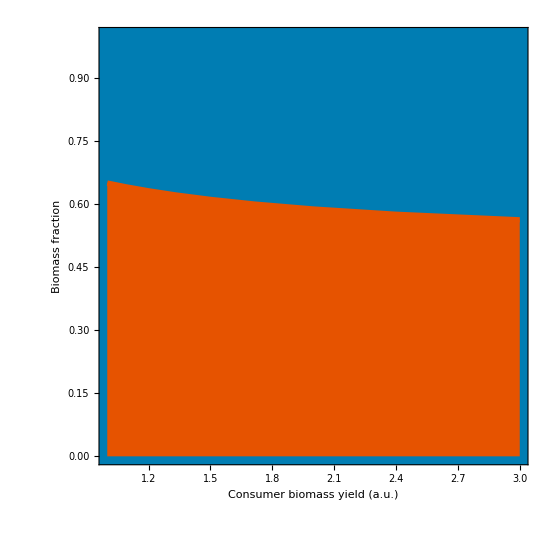

```mathematica
ListLinePlot[{Yieldinit/YxBRBv,λ/λinityield}/.OptimisationProblemSolvarYield,FrameLabel->{"Consumer biomass yield (a.u.)","Growth rate (a.u.)"},Joined->True,Prolog->StandardProlog,PlotStyle->{ColorData[68,"ColorList"][[3]],Thickness[0.007]},ImagePadding->{{80,15},{70,10}}]

ListLinePlot[{Yieldinit/YxBRBv,p1v/p1inityield}/.OptimisationProblemSolvarYield,FrameLabel->{"Consumer biomass yield (a.u.)","P_1 concentration (a.u.)"},Joined->True,Prolog->StandardProlog,PlotStyle->{ColorData[68,"ColorList"][[1]],Thickness[0.007]},ImagePadding->{{80,15},{70,10}}]

ListLinePlot[{Yieldinit/YxBRBv,BA0/(BA0+BiomB)}/.OptimisationProblemSolvarYield/.Params1varYield,FrameLabel->{"Consumer biomass yield (a.u.)","Biomass fraction"},Joined->True,FrameStyle->Directive[Black,22,Thickness->0.005],PlotRangePadding->0,PlotStyle->{ColorData[68,"ColorList"][[2]],Thickness[0.007]},Filling->Bottom,PlotRange->{All,{0,1}},FillingStyle->{ColorData[68,"ColorList"][[2]]},Prolog->{ColorData[68,"ColorList"][[1]],Rectangle[{-1,-1},{8,2}]},ImagePadding->{{80,15},{70,10}}]
```

## Model and results for division of labour

To model division of labour we extend the reaction network from the previous models to larger catabolic pathways. We run the corresponding optimisation problems both as function of the substrate concentration S and as function of the affinity of the consumer. In both cases, this requires the definition of new rate equations and a corresponding extended set of parameters. For more details, see the Supplementary Appendices.

### Division of labour as function of substrate concentration S

#### Rate equations and model parameters

```mathematica
v1Adol=v[k1A,sA,p1,e1Adol,2,1,Keq];
v2Adol=v[k2A,p1,xB,e2A,1,2,Keq];
v3Adol=v[k3A,xB,p2,e3A,2,1,Keq];

v1Bdol=v[k1B,xB,p2,e1B,1,2,Keq];

ParamsdolvarS={p2->0.01,
Keq->10^2,KeqT->1,
m1A->1,m3A->1,mRA->700,
m1B->1,mRB->700,
YsARA->200,Yp1sA->1,
YxBp1->1,YxBRB->200,
eTotA->1,eTA->0.1,
eTotB->1,
kTA->1000,k1A->1000,k2A->300,k3A->300,kRA->0.089,fRA->0.8,
kuB->1000,k1B->500,kRB->0.089,fRB->0.8,
BA0->1};
```

#### Optimisation problem: Maximise the growth rate of the producer for varying substrate concentration

```mathematica
ModelEquationsJoineddolvarS[sv_]:=Join[{Evaluate[vRA/eTotA]},
{(*Positivity constraints*)sA>=0,p1>=0,xB>=0,e1A>=0,e1Adol>=0,e2A>=0,e3A>=0,eRA>=0,euB>=0,e1B>=0,eRB>=0,BB0>=0,
(*Enzyme constraints*)eTA+e1A+e1Adol+e2A+e3A+eRA<=eTotA,euB+e1B+eRB<=eTotB,
(*Steady states*)vTA==v1A+v1Adol+YsARA vRA,Yp1sA v1Adol==v2Adol,YxBp1 v2Adol==v3Adol,mRA vRA== m1A v1A+m1A v1Adol+ m3A v3Adol,BA0 Yp1sA v1A==BB0 vuB,YxBp1 vuB==v1Bdol+YxBRB vRB,mRB vRB==m1B v1Bdol,
(*Biomass relation*)BA0 Yp1sA v1A/vRA ==BB0/YxBp1 eTotB/eTotA(mRB/m1B+YxBRB)}]/.{s->sv}
OptimisationProblemFuncdolvarS[sv_?NumericQ]:=NMaximize[ModelEquationsJoineddolvarS[sv]/.ParamsdolvarS,{sA,p1,xB,e1A,e1Adol,e2A,e3A,eRA,eRB,euB,e1B,BB0}]
```

#### Results

We run the optimisation problem for different values of the affinity of the consumer. After obtaining the results, we normalise the S concentration and the growth rate relative to the point where the shift from mode 2 to mode 1 initiates.

```mathematica
sstartOptdol=0.01;
sendOptdol=1.8;
sstepOptdol=0.03;
OptimisationProblemSoldolvarS=Table[{s->sval,{λA->vRA/eTotA,λB->vRB/eTotB,BiomB->BB0,e1->e1A,e2->e1Adol+e2A+e3A,eRiboA->eRA}/.OptimisationProblemFuncdolvarS[sval][[2]]/.ParamsdolvarS/.{s->sval}}//Flatten,{sval,sstartOptdol,sendOptdol,sstepOptdol}];
OptimisationProblemSoldolvarScorrec=OptimisationProblemSoldolvarS/. r_List/;Abs[BiomB/. r]<10^-5:>(r/. (λB->_):>(λB->0));
```

```mathematica
Scritdol=s/. Last@Select[OptimisationProblemSoldolvarScorrec,(λB/. #)==0&];
Sendshiftdol=s/. First@Select[OptimisationProblemSoldolvarScorrec,(e2/. #)<0.0001&];
λAcritdol=λA/. Last@Select[OptimisationProblemSoldolvarScorrec,(λB/. #)==0&];
```

#### Figures

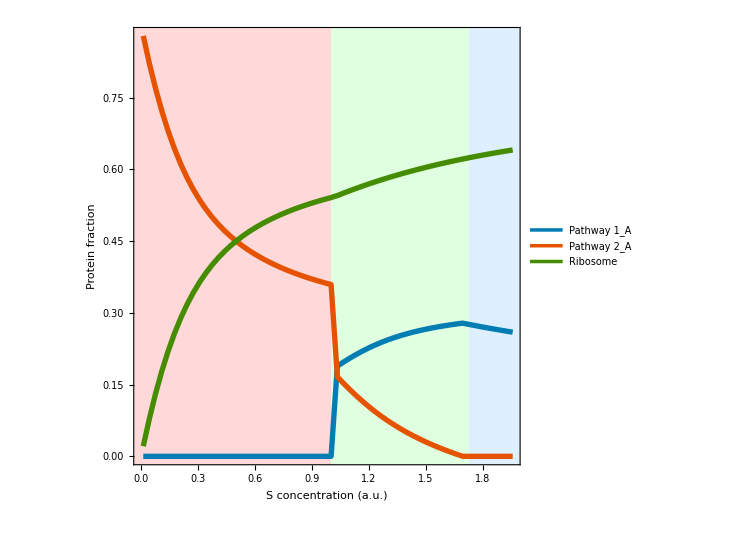

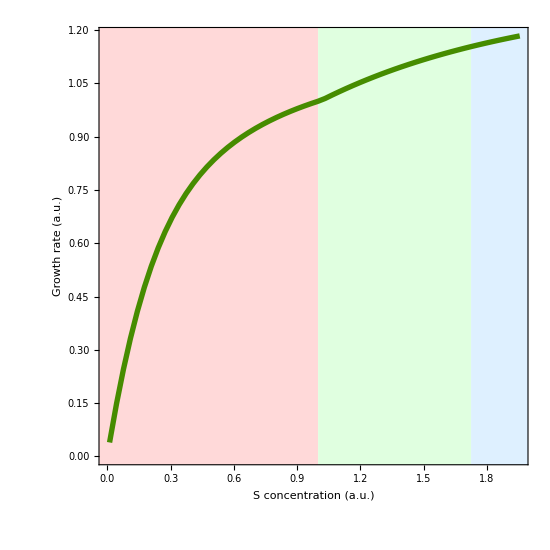

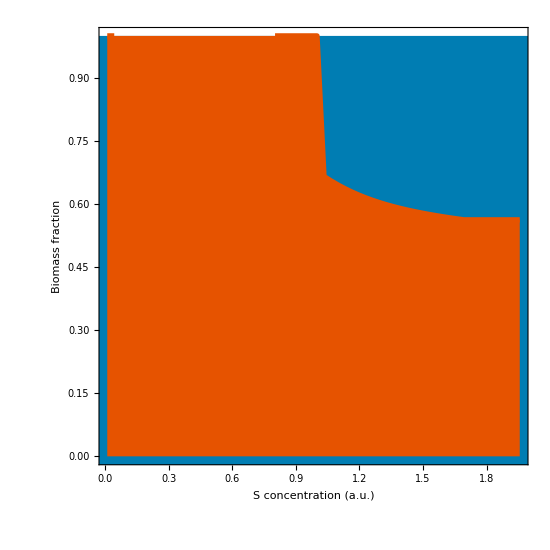

```mathematica
ListLinePlot[{{s/Scritdol,e1}/.OptimisationProblemSoldolvarScorrec,{s/Scritdol,e2}/.OptimisationProblemSoldolvarScorrec,{s/Scritdol,eRiboA}/.OptimisationProblemSoldolvarScorrec},FrameLabel->{"S concentration (a.u.)","Protein fraction"},PlotLegends->Placed[PointLegend[{"Pathway 1_A","Pathway 2_A","Ribosome"},LegendFunction->"Frame",LabelStyle->{FontFamily->"Helvetica",FontSize->18},LegendMarkerSize->{20,15}],{0.3,0.8}],PlotStyle->{{ColorData[68,"ColorList"][[1]],Thickness[0.007]},{ColorData[68,"ColorList"][[2]],Thickness[0.007]},{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{-1,-1},{1,2}]},{LightGreen,Rectangle[{1,-1},{Sendshiftdol/Scritdol,2}]},{LightBlue,Rectangle[{Sendshiftdol/Scritdol,-1},{8,2}]}},ImagePadding->{{70,10},{70,10}}]

ListLinePlot[{{s/Scritdol,λA/λAcritdol}/.OptimisationProblemSoldolvarScorrec},FrameLabel->{"S concentration (a.u.)","Growth rate (a.u.)"},PlotStyle->{{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{-1,-1},{1,2}]},{LightGreen,Rectangle[{1,-1},{Sendshiftdol/Scritdol,2}]},{LightBlue,Rectangle[{Sendshiftdol/Scritdol,-1},{8,2}]}},ImagePadding->{{70,10},{70,10}}]

biomassplotSconcDOL=ListLinePlot[{s/Scritdol,BA0/(BA0+BiomB)}/.OptimisationProblemSoldolvarScorrec/.ParamsdolvarS,FrameLabel->{"S concentration (a.u.)","Biomass fraction"},PlotRange->{All,{0,1}},PlotRangePadding->0,FrameStyle->Directive[Black,40,Thickness->0.005],PlotStyle->{ColorData[68,"ColorList"][[2]],Thickness[0.007]},Filling->Bottom,FillingStyle->{ColorData[68,"ColorList"][[2]]},Prolog->{ColorData[68,"ColorList"][[1]],Rectangle[{-1,-1},{3,1}]}]
```

### Division of labour as function of affinity of the consumer for its carbon substrate P_1

Here we simulate the division of labour model as function of the affinity of the consumer. Again, this requires a new definition for some rate equations and corresponding parameters. Qualitatively, this results in the same plots as for facultative syntrophy.

#### Rate equations and model parameters

```mathematica
v1AdolKm=v[k1A,sA,p1,e1Adol,2,0.01,Keq];

ParamsdolvarKm={s->0.8,p2->0.01,
Keq->10,KeqT->1,
m1A->1,m3A->1,mRA->700,
m1B->1,mRB->700,
YsARA->200,Yp1sA->1,
YxBp1->1,YxBRB->200,
eTotA->1,eTA->0.1,
eTotB->1,
kTA->1000,k1A->1000,k2A->300,k3A->300,kRA->0.089,fRA->0.8,
kuB->1000,k1B->500,kRB->0.089,fRB->0.8,
BA0->1};
```

#### Optimisation problem: Maximise the growth rate of the producer for varying affinity of the consumer

```mathematica
ModelEquationsJoineddolvarKm[Kminv_]:=Join[{Evaluate[vRA/eTotA]},
{(*Positivity constraints*)sA>=0,p1>=0,xB>=0,e1A>=0,e1Adol>=0,e2A>=0,e3A>=0,eRA>=0,euB>=0,e1B>=0,eRB>=0,BB0>=0,
(*Enzyme constraints*)eTA+e1A+e1Adol+e2A+e3A+eRA<=eTotA,euB+e1B+eRB<=eTotB,
(*Steady states*)vTA==v1AKm+v1AdolKm+YsARA vRA,Yp1sA v1AdolKm==v2Adol,YxBp1 v2Adol==v3Adol,mRA vRA== m1A v1AKm+m1A v1AdolKm+ m3A v3Adol,BA0 Yp1sA v1AKm==BB0 vuBKm,YxBp1 vuBKm==v1Bdol+YxBRB vRB,mRB vRB==m1B v1Bdol,
(*Biomass relation*)BA0 Yp1sA v1AKm/vRA ==BB0/YxBp1 eTotB/eTotA(mRB/m1B+YxBRB)}]/.{Km->Kminv}
OptimisationProblemFuncdolvarKm[Kminv_?NumericQ]:=NMaximize[ModelEquationsJoineddolvarKm[Kminv]/.ParamsdolvarKm,{sA,p1,xB,e1A,e1Adol,e2A,e3A,eRA,eRB,euB,e1B,BB0}]
```

#### Results

We run the optimisation problem for different values of the affinity of the consumer. After obtaining the results, we normalise the growth rate relative to the point where the switch initiates.

```mathematica
OptimisationProblemSoldolvarKm=Table[{Kminv->Kminvval,{p1v->p1,λA->vRA/eTotA,λB->vRB/eTotB,BiomB->BB0,e1->e1A,e2->e1Adol+e2A+e3A,eRiboA->eRA}/.OptimisationProblemFuncdolvarKm[Kminvval][[2]]/.ParamsdolvarKm/.{Kminv->Kminvval}}//Flatten,{Kminvval,{0.005,0.01,0.05,0.1,0.15,0.18,0.2,0.22,0.23,0.25,0.26,0.27,0.28,0.3,0.5,0.8,1,2,5,10}}];
OptimisationProblemSoldolvarKmcorrec=OptimisationProblemSoldolvarKm/. r_List/;Abs[BiomB/. r]<10^-6:>(r/. {(λB->_):>(λB->0),(p1v->_):>(p1v->0)});
```

```mathematica
λswitchdolKm=λA/.Last@Select[OptimisationProblemSoldolvarKmcorrec,(λB/. #)==0&];
KminvswitchdolKm=Kminv/.Last@Select[OptimisationProblemSoldolvarKmcorrec,(λB/. #)==0&];
```

#### Figures

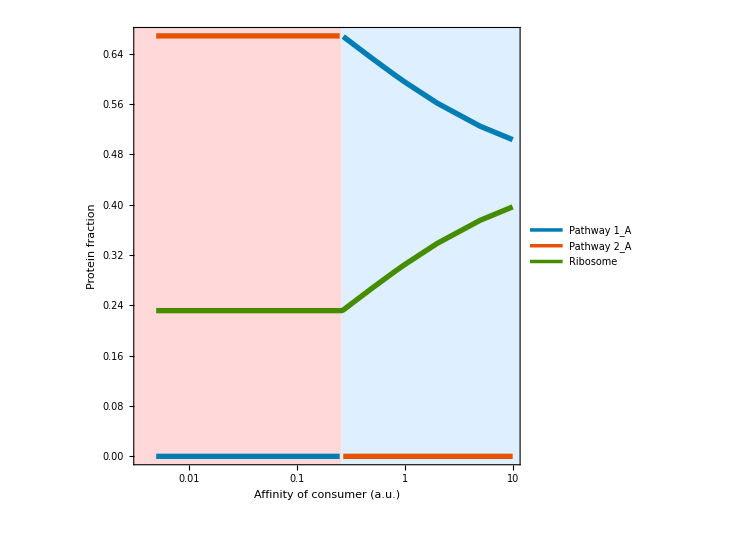

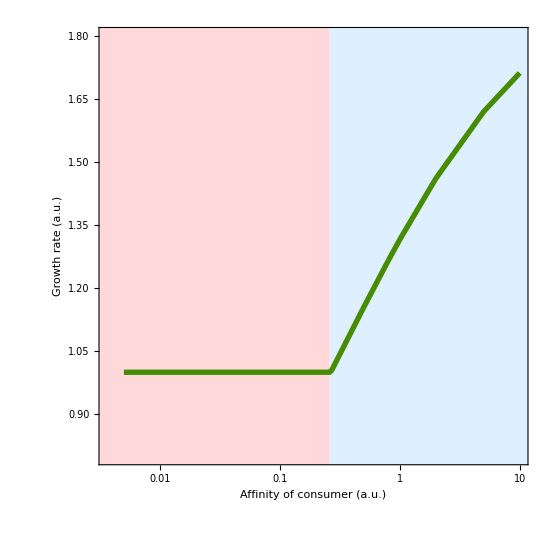

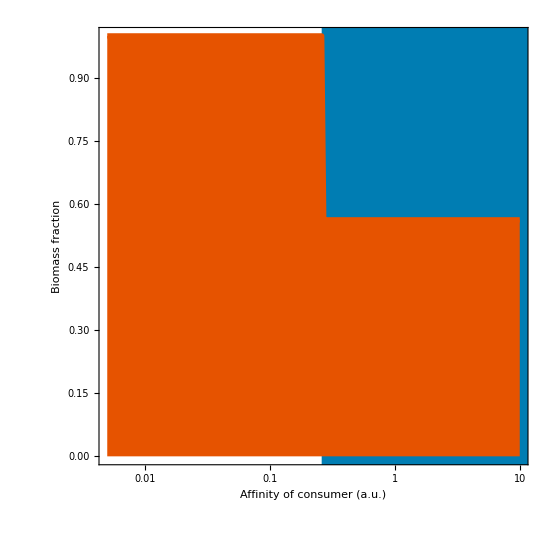

```mathematica
ListLogLinearPlot[{{Kminv,e1}/.OptimisationProblemSoldolvarKmcorrec/.{x_,y_}/;x==KminvswitchdolKm->{x,Indeterminate},{Kminv,e2}/.OptimisationProblemSoldolvarKmcorrec/.{x_,y_}/;x==KminvswitchdolKm->{x,Indeterminate},{Kminv,eRiboA}/.OptimisationProblemSoldolvarKmcorrec},FrameLabel->{"Affinity of consumer (a.u.)","Protein fraction"},Joined->True,PlotLegends->Placed[PointLegend[{"Pathway 1_A","Pathway 2_A" ,"Ribosome"},LegendFunction->"Frame",LabelStyle->{FontFamily->"Helvetica",FontSize->18},LegendMarkerSize->{20,15}],{0.2,0.6}],PlotStyle->{{ColorData[68,"ColorList"][[1]],Thickness[0.007]},{ColorData[68,"ColorList"][[2]],Thickness[0.007]},{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{Log[0.0001],-1},{Log[KminvswitchdolKm],2}]},{LightBlue,Rectangle[{Log[KminvswitchdolKm],-1},{8,2}]}},ImagePadding->{{70,10},{70,10}}]

ListLogLinearPlot[{{Kminv,λA/λswitchdolKm}/.OptimisationProblemSoldolvarKmcorrec},Joined->True,PlotRange->{All,{0.8,1.8}},FrameLabel->{"Affinity of consumer (a.u.)","Growth rate (a.u.)"},PlotStyle->{{ColorData[68,"ColorList"][[3]],Thickness[0.007]}},Prolog->{{LightRed,Rectangle[{Log[0.0001],-1},{Log[KminvswitchdolKm],2}]},{LightBlue,Rectangle[{Log[KminvswitchdolKm],-1},{8,2}]}},ImagePadding->{{70,10},{70,10}}]

biomassplotKmDOL=ListLogLinearPlot[{Kminv,BA0/(BA0+BiomB)}/.OptimisationProblemSoldolvarKmcorrec/.ParamsdolvarKm,Joined->True,FrameLabel->{"Affinity of consumer (a.u.)","Biomass fraction"},PlotRange->{All,{0,1}},PlotRangePadding->0,PlotStyle->{ColorData[68,"ColorList"][[2]],Thickness[0.007]},Filling->Bottom,FillingStyle->{ColorData[68,"ColorList"][[2]]},FrameStyle->Directive[Black,40,Thickness->0.005],Prolog->{ColorData[68,"ColorList"][[1]],Rectangle[{Log[KminvswitchdolKm],-1},{8,2}]}]
```